```mathematica
A0=100;
B0:=0.04;
h0:=2.3;
basal0:=0.1;
A1:=184;
B1:=0.007;
h1:=0.89;
basal1:=1.98;
A2:=57.6;
B2:=160;
h2:=3.7;
basal2:=0.52;
Aa:=0.9;
Ba:=0.072;
ha:=1.9;
basala:=0.105;
b0:=10;
b1:=43;
b2:=6;
etaN:=0;
etaG:=0.652;

Np:=1;
kr:=1/(5*60);
k:=b0*kr;
g:=1/(30*60);
f0[IPTG_]:=A0/(1+(IPTG/B0)^h0)+basal0;
f1[y0A_]:=A1/(1+(y0A/B1)^h1)+basal1;
f2[y1A_]:=A2/(1+(y1A/B2)^h2)+basal2;
fa[ATC_]:=Aa/(1+(ATC/Ba)^ha)+basala;
```

```mathematica
y0s:=k/g;
y0As[IPTG_]:=f0[IPTG]*y0s;
y1s[IPTG_]:=(Np*f1[y0As[IPTG]])/g;
y2s[IPTG_]:=(Np*f2[y1s[IPTG]])/g;
eta2int0:=(b0+1)/y0s;
eta2int1[IPTG_]:=(b1+1)/y1s[IPTG];
eta2int2[IPTG_]:=(b2+1)/y2s[IPTG];
```

```mathematica
H10[IPTG_]:=h1/(A1*f1[y0As[IPTG]])*(f1[y0As[IPTG]]-basal1)*(basal1+A1-f1[y0As[IPTG]]);
H21[IPTG_]:=h2/(A2*f2[y1s[IPTG]])*(f2[y1s[IPTG]]-basal2)*(basal2+A2-f2[y1s[IPTG]]);
eta20:=eta2int0+etaG^2;
eta21[IPTG_]:=eta2int1[IPTG]+1/2*(H10[IPTG])^2*eta20+1/2 etaN^2+etaG^2*(1-H10[IPTG]);
eta22[IPTG_]:=eta2int2[IPTG]+1/2*(H21[IPTG])^2*eta21[IPTG]+1/8*(H21[IPTG])^2*(H10[IPTG])^2*eta20+etaN^2*(1/2+1/8*(H21[IPTG])^2-3/4*H21[IPTG])+etaG^2*(1-H21[IPTG]-1/4*(H21[IPTG])^2*H10[IPTG]+1/2*H21[IPTG]*H10[IPTG]);
```

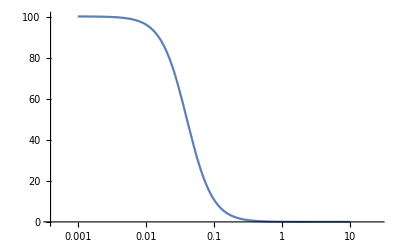

```mathematica
LogLinearPlot[f0[IPTG],{IPTG,10^-3,10}]
```

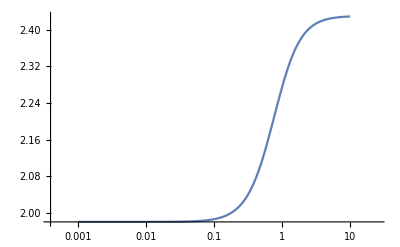

```mathematica
LogLinearPlot[f1[y0As[IPTG]],{IPTG,10^-3,10}]
```

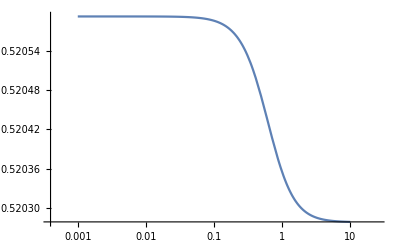

```mathematica
LogLinearPlot[f2[y1s[IPTG]],{IPTG,10^-3,10}]
```

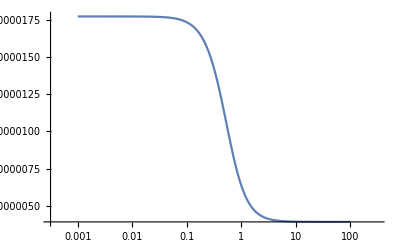

```mathematica
LogLinearPlot[(H21[IPTG])^2,{IPTG,10^-3,100}]
```